```mathematica
Q=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
Ime=(r0+xs)Cos[theta]+ys Sin[theta]-xd;


f=ArcTan[(xs Cos[theta]+(r0+ys) Sin[theta]-xd)/((r0+xs)Cos[theta]+ys Sin[theta]-xd)];

T=2 Pi;
omega=2 Pi /T;
k=0;

(Ime Q)/(Ime^2+0.28125 Q^2)
(*a0=2/T Integrate[f  ,{theta ,-Pi,Pi}] *)
```

((-0.1+2.4 Cos[theta]) (-0.1+2.4 Sin[theta]))/((-0.1+2.4 Cos[theta])^2+0.28125 (-0.1+2.4 Sin[theta])^2)

```mathematica
TrigReduce[((-xd+(r0) Cos[theta]) (-xd+0 Cos[theta]+(r0+0) Sin[theta]))/((-xd+(r0+0) Cos[theta]+0 Sin[theta])^2+0.28125 (-xd+0 Cos[theta]+(r0+0) Sin[theta])^2)]
```

(1.3913 (2. xd^2-2. r0 xd Cos[theta]-2. r0 xd Sin[theta]+1. r0^2 Sin[2 theta]))/(1.78261 r0^2+3.56522 xd^2-5.56522 r0 xd Cos[theta]+1. r0^2 Cos[2 theta]-1.56522 r0 xd Sin[theta])

```mathematica
Simplify[%10]
```

(xd (2.78261 xd-2.78261 r0 Sin[theta])+r0 Cos[theta] (-2.78261 xd+2.78261 r0 Sin[theta]))/(1.78261 r0^2+3.56522 xd^2-5.56522 r0 xd Cos[theta]+1. r0^2 Cos[2 theta]-1.56522 r0 xd Sin[theta])

```mathematica
Simplify[%8]
```

(0.780488 xd^2+0.390244 r0 xs+0.390244 xs^2+0.390244 r0 ys+0.390244 ys^2+(0.390244 r0 xs+0.390244 xs^2-0.390244 r0 ys-0.390244 ys^2) Cos[2 theta]-0.780488 r0 xd Sin[theta]-1.56098 xd ys Sin[theta]+Cos[theta] (-0.780488 r0 xd-1.56098 xd xs+(0.780488 r0^2+0.780488 r0 xs+0.780488 r0 ys+1.56098 xs ys) Sin[theta]))/(0.5 r0^2+1. xd^2+0.780488 r0 xs+0.5 xs^2+0.219512 r0 ys+0.5 ys^2+(0.280488 r0^2+0.780488 r0 xs+0.5 xs^2-0.219512 r0 ys-0.5 ys^2) Cos[2 theta]-0.439024 r0 xd Sin[theta]-2. xd ys Sin[theta]+Cos[theta] (-1.56098 r0 xd-2. xd xs+(0.439024 r0 xs+1.56098 r0 ys+2. xs ys) Sin[theta]))

-ⅈ Log[(-0.1+2.4 Cos[theta]+ⅈ (-0.1+2.4 Sin[theta]))/(√((-0.1+2.4 Cos[theta])^2+(-0.1+2.4 Sin[theta])^2))]

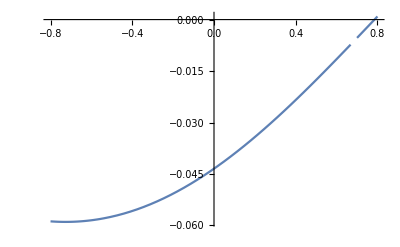

```mathematica
Q=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
Ime=(r0+xs)Cos[theta]+ys Sin[theta]-xd;

(*f=(Ime Q)/(Ime^2+0.28125 Q^2);
Integrate[f ,{theta ,-0.6 ,0.6}]
Plot[f-theta,{theta,-0.6,0.6}]*)


f1=-I Log[(Ime+I Q)/(Sqrt[Q^2+Ime^2])]
Plot[f1-theta,{theta,-0.8 ,0.8}]
```

```mathematica
Simplify[-ⅈ Log[(-xd+xs Cos[theta]+(r0+ys) Sin[theta]+ⅈ (-xd+(r0+xs) Cos[theta]+ys Sin[theta]))/(√((-xd+(r0+xs) Cos[theta]+ys Sin[theta])^2+(-xd+xs Cos[theta]+(r0+ys) Sin[theta])^2))]]
```

-ⅈ Log[((-1-ⅈ) xd+(ⅈ r0+(1+ⅈ) xs) Cos[theta]+(r0+(1+ⅈ) ys) Sin[theta])/(√((-xd+(r0+xs) Cos[theta]+ys Sin[theta])^2+(-xd+xs Cos[theta]+(r0+ys) Sin[theta])^2))]

```mathematica
a = 1;
b = 2;
z = a+I b;
Plot[a+I*b]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[a+ⅈ b]

```mathematica
Q=(r0) Sin[theta]-xd;
Ime=(r0+0)Cos[theta]+0 Sin[theta]-xd;

x=Q/Ime;
Simplify[TrigExpand[x-x^3/3]]
xx=Ime/Q;
Simplify[Pi/2-xx+xx^-3/3]
```

(2 xd^3-6 r0 xd^2 Cos[theta]+3 r0^2 xd Cos[2 theta]+3 r0^2 xd Sin[2 theta]-r0^3 Sin[3 theta])/(3 (xd-r0 Cos[theta])^3)

π/2+(-xd+r0 Cos[theta])/(xd-r0 Sin[theta])+(xd-r0 Sin[theta])^3/(3 (xd-r0 Cos[theta])^3)

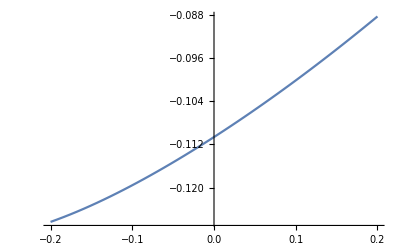

```mathematica
xd=0.1;
r0=1;

Plot[x-x^3/3-theta,{theta, -0.2,0.2}]
(*Plot[Pi/2-1/x+1/(3 x^3)-theta,{theta, Pi/4+0.001,1.2}]*)
```

0.1

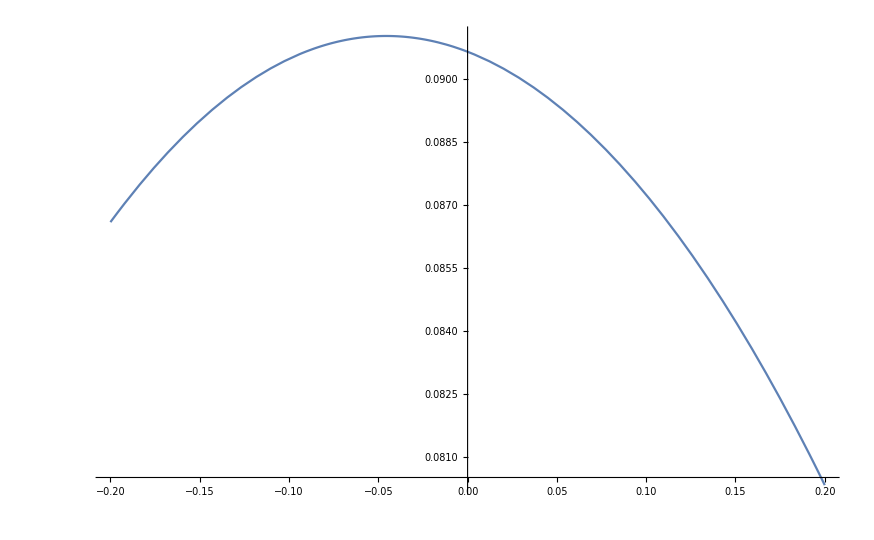

```mathematica
Q=xs Cos[theta]+(r0+ys) Sin[theta];
Ime=(r0+xs)Cos[theta]+ys Sin[theta];
z=Q/Ime;
xs=0.1;
ys=0.1

Plot[z-z^3/3-theta,{theta,-0.2,0.2}]
```

```mathematica
theta=Pi/4+0.0001;
(Pi/2+1/x-1/(3 x^3))
theta=Pi/4-0.0001;
x-x^3/3
```

2/3+π/2

2/3

```mathematica
Q=xs Cos[theta]+(r0+ys) Sin[theta]-xd;
Ime=(r0+xs)Cos[theta]+ys Sin[theta]-xd;


Q=(r0+ys) Sin[theta];
Ime=(r0)Cos[theta]+ys Sin[theta];

x=Q/Ime;
xxx=x^3/3;

Simplify[TrigExpand[x+xxx]]
```

((r0+ys) Sin[theta] (2 r0^2+r0 ys+2 ys^2+(r0^2-r0 ys-2 ys^2) Cos[2 theta]+3 r0 ys Sin[2 theta]))/(3 (r0 Cos[theta]+ys Sin[theta])^3)

```mathematica
TrigReduce[((r0+ys) Sin[theta] (2 r0^2+r0 ys+2 ys^2+(r0^2-r0 ys-2 ys^2) Cos[2 theta]+3 r0 ys Sin[2 theta]))/(3 (r0 Cos[theta]+ys Sin[theta])^3)]
```

(2 (3 r0^2 ys Cos[theta]+3 r0 ys^2 Cos[theta]-3 r0^2 ys Cos[3 theta]-3 r0 ys^2 Cos[3 theta]+3 r0^3 Sin[theta]+6 r0^2 ys Sin[theta]+9 r0 ys^2 Sin[theta]+6 ys^3 Sin[theta]+r0^3 Sin[3 theta]-3 r0 ys^2 Sin[3 theta]-2 ys^3 Sin[3 theta]))/(3 (3 r0^3 Cos[theta]+3 r0 ys^2 Cos[theta]+r0^3 Cos[3 theta]-3 r0 ys^2 Cos[3 theta]+3 r0^2 ys Sin[theta]+3 ys^3 Sin[theta]+3 r0^2 ys Sin[3 theta]-ys^3 Sin[3 theta]))

```mathematica
Simplify[%18]
```

((r0+ys) Sin[theta] (2 r0^2+r0 ys+2 ys^2+(r0^2-r0 ys-2 ys^2) Cos[2 theta]+3 r0 ys Sin[2 theta]))/(3 (r0 Cos[theta]+ys Sin[theta])^3)

```mathematica
TrigReduce[(r0 Cos[theta]+ys Sin[theta])^3]
```

1/4 (3 r0^3 Cos[theta]+3 r0 ys^2 Cos[theta]+r0^3 Cos[3 theta]-3 r0 ys^2 Cos[3 theta]+3 r0^2 ys Sin[theta]+3 ys^3 Sin[theta]+3 r0^2 ys Sin[3 theta]-ys^3 Sin[3 theta])

```mathematica
Q=xs Cos[theta]+(r0) Sin[theta];
Ime=(r0+xs)Cos[theta];

x=Q/Ime;
xxx=x^3/3;
Simplify[TrigExpand[x+xxx]]
```

(Sec[theta]^3 (3 xs (2 r0^2+3 r0 xs+2 xs^2) Cos[theta]+xs^2 (3 r0+2 xs) Cos[3 theta]+2 r0 (2 r0^2+3 r0 xs+3 xs^2+(r0^2+3 r0 xs+3 xs^2) Cos[2 theta]) Sin[theta]))/(6 (r0+xs)^3)

```mathematica
Expand[(3 xs (2 r0^2+3 r0 xs+2 xs^2) +xs^2 (3 r0+2 xs) +2 r0 (2 r0^2+3 r0 xs+3 xs^2+(r0^2+3 r0 xs+3 xs^2) ) theta)/(6 (r0+xs)^3)]
```

(r0^3 theta)/(r0+xs)^3+(r0^2 xs)/(r0+xs)^3+(2 r0^2 theta xs)/(r0+xs)^3+(2 r0 xs^2)/(r0+xs)^3+(2 r0 theta xs^2)/(r0+xs)^3+(4 xs^3)/(3 (r0+xs)^3)